Numerical evoluation of p_(0,s) coefficients (without the overall factor of 2πω)

```mathematica
f[e_,s_]:=NIntegrate[Exp[I*s*(u-e*Sin[u])]/(1-e*Cos[u])^2, {u, 0, 2π}]
```

Analytical expression of p_(0,s) coefficients (without the overall factor of 2πω)

```mathematica
g[e_,s_]:=Integrate[Exp[I*s*(u-e*Sin[u])]/(1-e*Cos[u])^2, {u, 0, 2π},Assumptions->{Element[e,Reals], e>0}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76692×10^-13-2.77556×10^-17 ⅈ and 1.36788×10^-12 for the integral and error estimates.

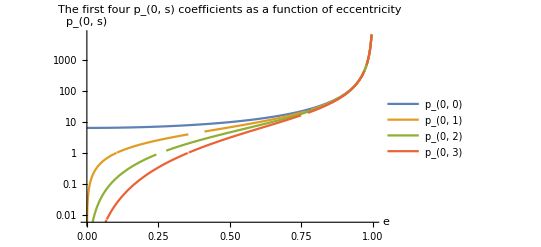

```mathematica
LogPlot[{f[e, 0],f[e,1], f[e, 2], f[e, 3]}, {e, 0, 1}, PlotLegends->{"p_(0, 0)","p_(0, 1)","p_(0, 2)","p_(0, 3)"},PlotLabel->Style["The first four p_(0, s) coefficients as a function of eccentricity",FontSize->32],AxesLabel->{Style["e",FontSize->24],Style["p_(0, s)",FontSize->24]}]
```

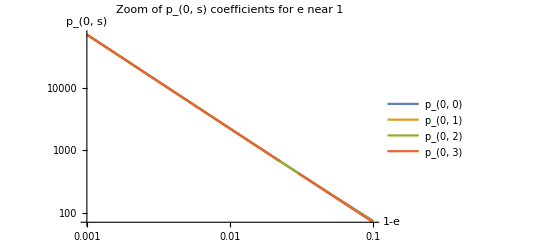

```mathematica
LogLogPlot[{f[1-x, 0],f[1-x,1],f[1-x,2],f[1-x,3]},{x,10^-3,10^-1},PlotPoints->100,PlotLegends->{"p_(0, 0)","p_(0, 1)","p_(0, 2)","p_(0, 3)"},PlotLabel->Style["Zoom of p_(0, s) coefficients for e near 1",FontSize->32],AxesLabel->{Style["1-e",FontSize->24],Style["p_(0, s)",FontSize->24]}]
```

```mathematica
The above look very linear, so check if the slope appears to be constant for e approaching 1
```

```mathematica
Limit[D[Log[g[1-Exp[-x],0]],x],x->Infinity]
```

3/2

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76692×10^-13-2.77556×10^-17 ⅈ and 1.36788×10^-12 for the integral and error estimates.

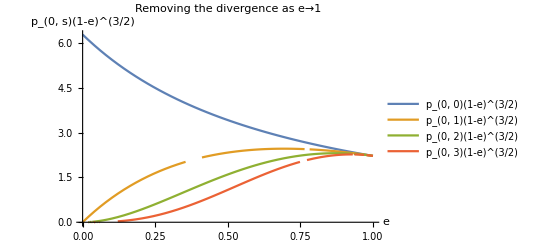

```mathematica
Plot[{f[e,0]*(1-e)^1.5,f[e,1]*(1-e)^1.5,f[e,2]*(1-e)^1.5,f[e,3]*(1-e)^1.5},{e,0,1},PlotLegends->{"p_(0, 0)(1-e)^(3/2)","p_(0, 1)(1-e)^(3/2)","p_(0, 2)(1-e)^(3/2)","p_(0, 3)(1-e)^(3/2)"},PlotLabel->Style["Removing the divergence as e→1",FontSize->32],AxesLabel->{Style["e",FontSize->24],Style["p_(0, s)(1-e)^(3/2)",FontSize->24]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76692×10^-13-2.77556×10^-17 ⅈ and 1.36788×10^-12 for the integral and error estimates.

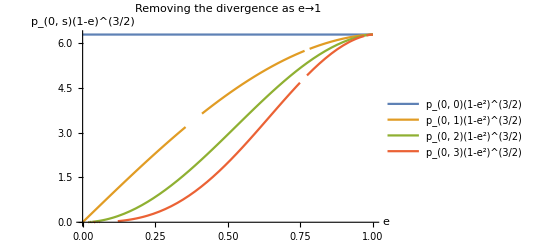

```mathematica
Plot[{f[e,0]*(1-e^2)^1.5,f[e,1]*(1-e^2)^1.5,f[e,2]*(1-e^2)^1.5,f[e,3]*(1-e^2)^1.5},{e,0,1},PlotLegends->{"p_(0, 0)(1-e^2)^(3/2)","p_(0, 1)(1-e^2)^(3/2)","p_(0, 2)(1-e^2)^(3/2)","p_(0, 3)(1-e^2)^(3/2)"},PlotLabel->Style["Removing the divergence as e→1",FontSize->32],AxesLabel->{Style["e",FontSize->24],Style["p_(0, s)(1-e)^(3/2)",FontSize->24]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853001364566677372607992192220043546624363983710281900130212}. NIntegrate obtained -6.33174×10^-16-2.23779×10^-16 ⅈ and 8.41455×10^-14 for the integral and error estimates.

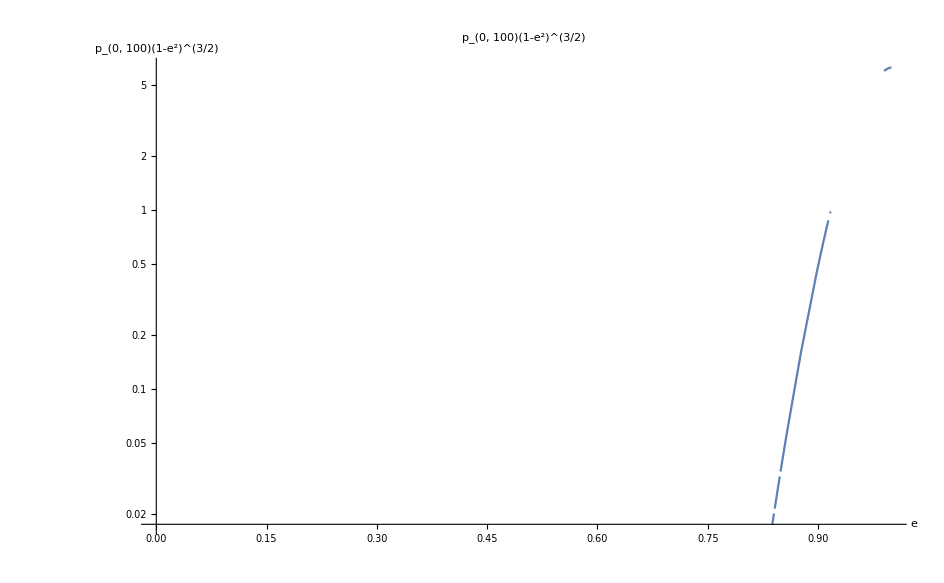

```mathematica
LogPlot[f[e,100]*(1-e^2)^1.5,{e,0,1},PlotLabel->Style["p_(0, 100)(1-e^2)^(3/2)",FontSize->32],AxesLabel->{Style["e",FontSize->24],Style["p_(0, 100)(1-e^2)^(3/2)",FontSize->24]}]
```

```mathematica
g[0.8,100]
```

```mathematica
Limit[g[1-x,0]*x^(3/2),x->0]
```

Indeterminate

```mathematica
Limit[f[e,0]*(1-e)^(3/2),e->1]
```

lim_(e→1) (1-e)^(3/2) f[e,0]

```mathematica
g[1-x,0]*x^(3/2)/.x->0.000001
```

2.22144+0. ⅈ

```mathematica
FullSimplify[Integrate[Cos[x]*Exp[-y]/(1-Cos[x]+Exp[-y]*Cos[x])^3, {x,0,2*π}]/Integrate[1/(1-Cos[x]+Exp[-y]*Cos[x])^2,{x,0,2*π}], Assumptions->{Element[y,Reals], y>0}]
```

(3 (-1+ⅇ^y))/(-2+4 ⅇ^y)

```mathematica
ArcSec[0.99]
```

0.+0.142014 ⅈ

```mathematica
Integrate[1/(1-y*Cos[x])^2,{x,0,2*π},Assumptions->{Element[y,Reals] && y>0 && y<1}]
```

(2 π)/((1-y^2)^(3/2))

```mathematica
g[y,0]
```

ConditionalExpression[(2 π)/((1-y^2)^(3/2)), y<1]

```mathematica
g[y,1]
```

Integrate[ⅇ^(ⅈ (u-y Sin[u]))/(1-y Cos[u])^2,{u,0,2 π},Assumptions→{y∈ℝ,y>0}]

```mathematica
2*π/2^1.5
```

2.22144